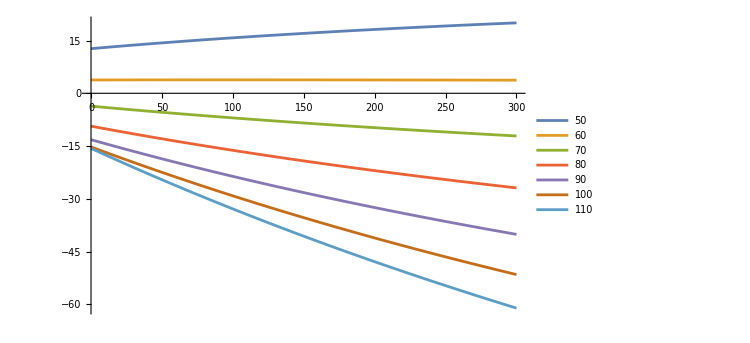

```mathematica
lengthFuselage[x_] := 130 + x;

centerMotor = 65;
centerFuselage[x_] := lengthFuselage[x]/2;
centerCone[x_] := 270 + x;
centerFins[r_] := r;

massMotor= 180;
massFuselage[x_] := 160/400 * lengthFuselage[x];
massCone = 280;

areaFins[r_] := Pi*r^2;
areaFuselage[x_] := lengthFuselage[x]*50;
areaCone = 280*85;

centerMass[x_] = (centerMotor*massMotor+ centerFuselage[x]*massFuselage[x] + centerCone[x] * massCone)/(massMotor + massFuselage[x] + massCone);

centerPressure[x_, r_] = (areaFins[r]*centerFins[r] + areaFuselage[x]*centerFuselage[x] + areaCone * centerCone[x])/(areaFins[r]+areaFuselage[x]+areaCone); 

delta[x_, r_] = centerPressure[x, r] - centerMass[x];

finRadius = {50, 60, 70, 80, 90, 100, 110};

Plot[Evaluate[delta[x, #] & /@ finRadius], {x, 0, 300}, PlotLegends-> finRadius]
```